1. Renormalization Group Recursive Equations Setup

```mathematica
dim=8;
Clear[μ,η];
A[6]=B[6]=μ;
A[7]=B[7]=η;
Z0[x0_,x1_,x2_,x3_,x4_]:=μ^(-(x0*x3+x1*x4)/2)*η^(-(x1+x3)/2)*Exp[-2*A[0]]*A[1]^(-((x0+x1)+(x1+x2)+(x2+x3)+(x3+x4))/2)*A[2]^(-((x0+x2)+(x2+x4))/2)*A[3]^(-(x0*x1+x1*x2+x2*x3+x3*x4)/2)*A[4]^(-(x0*x2+x2*x4)/2)*A[5]^(-(x0*x1*x2+x2*x3*x4)/2)
Z1[x0_,x2_,x4_]:=Exp[-B[0]]*B[1]^(-((x0+x2)+(x2+x4))/2)*B[2]^(-(x0+x4)/2)*B[3]^(-(x0*x2+x2*x4)/2)*B[4]^(-(x0*x4)/2)*B[5]^(-x0*x2*x4/2)
TrZ0[x0_,x2_,x4_]:=Sum[Sum[Z0[x0,x1,x2,x3,x4],{x1,-1,1,2}],{x3,-1,1,2}]
i=0;
For[x0=-1,x0<=1,x0+=2,
For[x2=-1,x2<=1,x2+=2,
For[x4=-1,x4<=1,x4+=2,
leq[i]=Z1[x0,x2,x4];
req[i++]=TrZ0[x0,x2,x4];
]
]
]
(*Equates the unrenormalized with the renormalized variables*)
req[0]==leq[0];
req[1]==leq[1];
req[2]==leq[2];
req[3]==leq[3];
req[4] == leq[4];
req[5] ==leq[5] ;
req[6] ==leq[6] ;
req[7] ==leq[7] ;
SB[0]=Simplify[Solve[Simplify[(Factor[leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7]])^(-1/8),Assumptions->B[0]>0]==Simplify[(Factor[req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7]])^(-1/8),Assumptions->η>0&&μ>0&& A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0],B[0]],Assumptions->C[1]==0&&η>0&&μ>0&& A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0][[1]];
SB[0]={B[0]-> 2*A[0]+(B[0]/.SB[0]/.A[0]->0)};
SB[1]=Simplify[Part[Solve[Simplify[((leq[0]*leq[1]*leq[1]*leq[5])^(1/4)/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/8)),Assumptions->(B[1]>0 && B[3]>0 && B[0]>0)]==Simplify[((req[0]*req[1]*req[1]*req[5])^(1/4)/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/8)),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[1]],1]];
SB[2]=Simplify[Part[Solve[Simplify[((leq[2]/leq[5]/leq[1])^(1/4)*(leq[0]/leq[1]*leq[2]*leq[3]*leq[4]/leq[5]*leq[6]/leq[7])^(1/8)),Assumptions->(B[1]>0 && B[3]>0 && B[0]>0&& B[2]>0&& B[4]>0&& B[5]>0)]==Simplify[((req[2]/req[5]/req[1])^(1/4)*(req[0]/req[1]*req[2]*req[3]*req[4]/req[5]*req[6]/req[7])^(1/8)),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[2]],1]];
SB[3]=Simplify[Part[Solve[Simplify[(leq[2]*leq[5]*leq[1]*leq[3])^(1/2)/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/4),Assumptions->(B[0]>0 && B[3]>0)]==Simplify[(req[2]*req[5]*req[1]*req[3])^(1/2)/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/4),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[3]],1]];
SB[4]=Simplify[Part[Solve[Simplify[(leq[1]*leq[3])/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/4),Assumptions->B[0]>0]==Simplify[(req[1]*req[3])/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/4),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[4]],1]];
SB[5]=Simplify[Part[Solve[Simplify[(leq[0]/leq[1]/leq[2]*leq[3])^(1/2)*((leq[2]*leq[5]*leq[1]*leq[3])^(1/2)/(leq[0]*leq[1]*leq[2]*leq[3]*leq[4]*leq[5]*leq[6]*leq[7])^(1/4)),Assumptions->(B[3]>0 && B[5]>0 && B[0]>0)]==Simplify[(req[0]/req[1]/req[2]*req[3])^(1/2)*((req[2]*req[5]*req[1]*req[3])^(1/2)/(req[0]*req[1]*req[2]*req[3]*req[4]*req[5]*req[6]*req[7])^(1/4)),Assumptions->(λ>0&&η>0 && μ>0 && A[0]>0 && A[1]>0 && A[2]>0 && A[3]>0 && A[4]>0 && A[5]>0)],B[5]],1]];
SBT=Table[Part[Factor[SB[n]],1],{n,0,5}];
```

2. One- and Two-Point Function Setup

```mathematica
Clear[μ,η]
SIC={B[0]->0,B[1]->1,B[2]->1,B[3]->μ,B[4]->1,B[5]->1};
InitRG:=SAT=Table[A[n]->B[n]/.SIC,{n,0,dim-1}];
RG:=SAT=Table[A[n]->B[n]/.Simplify[SBT/.SAT],{n,0,dim-1}];
W=Table[Factor[D[(B[i]/.SBT),A[j]]],{j,0,dim-1},{i,0,dim-1}];
InitRGW:=Block[{},
InitRG;
Υ=Array[KroneckerDelta,{dim,dim}];
];
RGW:=Block[{},
Υ=Together[Υ.(W/.SAT)];
RG;
];
LnZ1=-A[0]+Log[Sum[Sum[Sum[η^(-(x0+x1+x2)/2)*A[1]^(-((x0+x1)+(x1+x2))/2)*A[2]^(-(x0+x2)/2)*A[3]^(-(x0*x1+x1*x2)/2)*A[4]^(-(x0*x2)/2)*A[5]^(-(x0*x1*x2)/2),{x0,-1,1,2}],{x1,-1,1,2}],{x2,-1,1,2}]];
LnZ1=-A[0]+(LnZ1/.A[0]->0);
DLnZ1=Table[Factor[D[LnZ1,A[i]]],{i,0,dim-1}];
InitRGW;
dμdβ=-2μ;
dA0dμ=dμdβ*Table[D[A[i]/.SAT,μ],{i,0,dim-1}];
dηdH=-2η;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
Ω=Table[D[D[(B[j]/.SBT),A[i]],A[k]],{k,0,dim-1},{j,0,dim-1},{i,0,dim-1}];
InitRGΩ:=Block[{},InitRGW;
Λ=0*Array[KroneckerDelta,{dim,dim,dim}];
(*Λ=Table[D[Υ,A[j]],{j,0,dim-1}];
This is all zero,anyway!*)];
RGΩ:=Block[{},Λ=Together[Together[Λ.Together[W/.SAT]]+Transpose[Together[(Υ.Together[Ω/.SAT]).Transpose[Υ]],{1,3,2}]];
RGW;];
D2LnZ1=Factor[Table[D[DLnZ1,A[i]],{i,0,dim-1}]];
Clear[k,a,b,x,y,z]
θ[k_,x_,y_,z_]:=Block[{a,b},If[k==0,Return[η^(-(x+y+z)/2)*μ^(-(x*y+y*z)/2)],Return[Expand[η^(y/2)*Sum[Sum[μ^(-(x*b+a*z)/2)*θ[k-1,x,a,y]*θ[k-1,y,b,z],{a,-1,1,2}],{b,-1,1,2}]]]]]
Z[k_]:=If[k>0,Return[Sum[Sum[Sum[θ[k-1,x,y,z],{x,-1,1,2}],{y,-1,1,2}],{z,-1,1,2}]],Return[1]]
```

2.1 Partition function test

```mathematica
Clear[μ,η]
InitRG
Factor[FullSimplify[Exp[LnZ1]/.SAT,Assumptions->μ>0&&η>0]]
Factor[Z[1]]
Factor[%%/%]
```

{A[0]→0,A[1]→1,A[2]→1,A[3]→μ,A[4]→1,A[5]→1,μ→μ,η→η}

((1+η) (1-η+η^2+2 η μ+η μ^2))/(η^(3/2) μ)

((1+η) (1-η+η^2+2 η μ+η μ^2))/(η^(3/2) μ)

1

```mathematica
Clear[μ,η]
Z[2]
μ=1.4;
η=0.5;
InitRG;
RG;
Factor[(Exp[LnZ1]/.SAT)/Z[2]]
```

2/η^(3/2)+6/(√η)+6 √η+2 η^(3/2)+1/(η^(5/2) μ^3)+η^(5/2)/μ^3+3/(η^(3/2) μ)+(3 η^(3/2))/μ+(3 μ)/(√η)+3 √η μ+μ^3/(√η)+√η μ^3

1.

```mathematica
μ=1.68324;
η=0.9726;
InitRG;
RG;
RG;
RG;
Factor[FullSimplify[Exp[LnZ1]/.SAT,Assumptions->μ>0&&η>0]]
Factor[Z[4]]
Factor[%%/%]
```

371943.

371943.

1.

Test magnetization

```mathematica
Clear[μ,η]
dηdH=-2 η;
Factor[dηdH*D[Log[Z[1]],η]]
m21=Factor[(dηdH)^2*D[Log[Z[1]],{η,2}]/Z[1]]
```

-((-1+√η) (1+√η) (3+3 η+3 η^2+2 η μ+η μ^2))/((1+η) (1-η+η^2+2 η μ+η μ^2))

-1/((1+η)^3 (1-η+η^2+2 η μ+η μ^2)^3)2 η^(3/2) μ (-3-18 η^3+3 η^6-12 η μ-20 η^2 μ-12 η^4 μ+4 η^5 μ-6 η μ^2-14 η^2 μ^2-8 η^3 μ^2-2 η^4 μ^2+2 η^5 μ^2-4 η^2 μ^3-8 η^3 μ^3+4 η^4 μ^3-η^2 μ^4-2 η^3 μ^4+η^4 μ^4)

```mathematica
N[m21/.{η->1,μ->2},2]
```

0.21

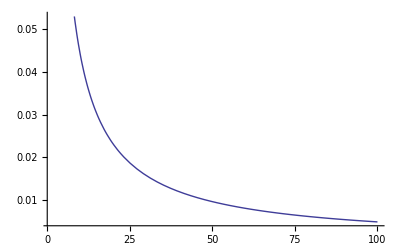

```mathematica
η=1;
Plot[-1/((1+η)^3 (1-η+η^2+2 η μ+η μ^2)^3)2 η^(3/2) μ (-3-18 η^3+3 η^6-12 η μ-20 η^2 μ-12 η^4 μ+4 η^5 μ-6 η μ^2-14 η^2 μ^2-8 η^3 μ^2-2 η^4 μ^2+2 η^5 μ^2-4 η^2 μ^3-8 η^3 μ^3+4 η^4 μ^3-η^2 μ^4-2 η^3 μ^4+η^4 μ^4),{μ,1,100}]
Clear[μ,η]
```

```mathematica
Clear[μ,η]
dηdH=-2 η;
Factor[dηdH*D[Log[Z[1]],η]]
m21=Factor[(dηdH)^2*D[Log[Z[2]],{η,2}]/Z[2]]
```

-((-1+√η) (1+√η) (3+3 η+3 η^2+2 η μ+η μ^2))/((1+η) (1-η+η^2+2 η μ+η μ^2))

-(2 η^(5/2) μ^3 (-5-50 η^5+5 η^10-30 η μ^2-102 η^4 μ^2-90 η^6 μ^2+18 η^9 μ^2-20 η μ^3-84 η^2 μ^3-132 η^3 μ^3-68 η^4 μ^3-60 η^6 μ^3-84 η^7 μ^3-12 η^8 μ^3+12 η^9 μ^3-69 η^2 μ^4-66 η^3 μ^4-162 η^5 μ^4-42 η^7 μ^4+21 η^8 μ^4-36 η^2 μ^5-108 η^3 μ^5-180 η^4 μ^5-216 η^5 μ^5-108 η^6 μ^5+36 η^7 μ^5+36 η^8 μ^5-26 η^2 μ^6-148 η^3 μ^6-246 η^4 μ^6-144 η^5 μ^6-90 η^6 μ^6+28 η^7 μ^6+10 η^8 μ^6-36 η^3 μ^7-96 η^4 μ^7-72 η^5 μ^7+12 η^7 μ^7-18 η^3 μ^8-39 η^4 μ^8-18 η^5 μ^8-9 η^6 μ^8+6 η^7 μ^8-12 η^3 μ^9-32 η^4 μ^9-24 η^5 μ^9+4 η^7 μ^9-6 η^4 μ^10-12 η^5 μ^10+6 η^6 μ^10-η^4 μ^12-2 η^5 μ^12+η^6 μ^12))/((1+η)^3 (1-η+η^2-η^3+η^4+3 η μ^2-3 η^2 μ^2+3 η^3 μ^2+2 η μ^3+4 η^2 μ^3+2 η^3 μ^3+3 η^2 μ^4+η^2 μ^6)^3)

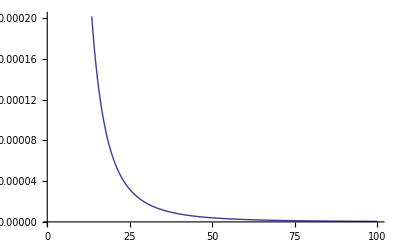

```mathematica
η=1;
Plot[-(2 η^(5/2) μ^3 (-5-50 η^5+5 η^10-30 η μ^2-102 η^4 μ^2-90 η^6 μ^2+18 η^9 μ^2-20 η μ^3-84 η^2 μ^3-132 η^3 μ^3-68 η^4 μ^3-60 η^6 μ^3-84 η^7 μ^3-12 η^8 μ^3+12 η^9 μ^3-69 η^2 μ^4-66 η^3 μ^4-162 η^5 μ^4-42 η^7 μ^4+21 η^8 μ^4-36 η^2 μ^5-108 η^3 μ^5-180 η^4 μ^5-216 η^5 μ^5-108 η^6 μ^5+36 η^7 μ^5+36 η^8 μ^5-26 η^2 μ^6-148 η^3 μ^6-246 η^4 μ^6-144 η^5 μ^6-90 η^6 μ^6+28 η^7 μ^6+10 η^8 μ^6-36 η^3 μ^7-96 η^4 μ^7-72 η^5 μ^7+12 η^7 μ^7-18 η^3 μ^8-39 η^4 μ^8-18 η^5 μ^8-9 η^6 μ^8+6 η^7 μ^8-12 η^3 μ^9-32 η^4 μ^9-24 η^5 μ^9+4 η^7 μ^9-6 η^4 μ^10-12 η^5 μ^10+6 η^6 μ^10-η^4 μ^12-2 η^5 μ^12+η^6 μ^12))/((1+η)^3 (1-η+η^2-η^3+η^4+3 η μ^2-3 η^2 μ^2+3 η^3 μ^2+2 η μ^3+4 η^2 μ^3+2 η^3 μ^3+3 η^2 μ^4+η^2 μ^6)^3),{μ,1,100}]
Clear[μ,η]
```

3. One Point Functions: IE and Mag

3.0 Ground State

```mathematica
Clear[μ,η];
InitRGW;
μ=N[10^9,1000];
η=1;
kmax=20;
GSVector=ConstantArray[0,{kmax-1}];
kind=1;
InitRGW;
For[i=2,i≤kmax,++i,
RGW;
Part[GSVector,kind]=N[(dA0dμ.Υ).(DLnZ1/.SAT),8];
kind++;
]
GSVector
```

{-6.,-10.,-22.,-46.,-94.,-188.,-378.,-758.,-1514.,-3030.,-6062.,-12126.,-24252.,-48506.,-97014.,-194026.,-388054.,-776110.,-1.552222×10^6}

3.1 Internal Energy

```mathematica
Clear[μ,η,IEc]
InitRGW;
(**Temperature for Mag, IE**)
precN=1000;
Tmin=0.011;
Tmax=10.006;
Tinc=0.01;
TVector=N[Prepend[Range[Tmin,Tmax,Tinc],0.01],precN];
μVector=N[Exp[2/TVector],precN];
μinvVector=1.0/μVector;
μiv=Range[Ceiling[Exp[-Max[2.0/Max[TVector]]]*1000]/1000.0,0.999999,0.005];
μiv=N[Join[μiv,{0.999999998}],precN];
μinvVector=N[Join[μinvVector,μiv],precN];
μVector=N[Join[μVector,1.0/μiv],precN];
μVector[[Dimensions[μVector][[1]]]]=1;
TVector=N[Join[TVector,2.0/Log[1/μiv]],precN];
Clear[μiv];
(*kVector={6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,32,64,100,128,200,256};*)
kVector=Range[5,20,1];
InitRGW;
dμdβ=-2 μ;
dA0dμ=dμdβ*Table[D[A[i]/.SAT,μ],{i,0,dim-1}];
η=N[1.0,precN];
IE=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[TVector][[1]]}];
μind=0;
Do[kind=1;
μind++;
μ=N[μVector[[μind]],precN];
InitRGW;
For[i=2,i≤Max[kVector],++i,RGW;
If[i==kVector[[kind]],Part[Part[IE,kind],μind]=N[1/(2^(i)+1)*(dA0dμ.Υ).(DLnZ1/.SAT),precN];kind++,];],
{Tx,1,Dimensions[μVector][[1]],1}
];
Rasterize[ListLinePlot[Table[Table[{1.0/μVector[[i]],IE[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=6","k=7","k=8","k=9"},PlotStyle->Thick,PlotRange->{{0,1},{-1.6,0}},AxesOrigin->{0,-1.5}]]
IEc=IE;
PrependTo[IEc,TVector];
PrependTo[IEc,1.0/μVector];
PrependTo[kVector,0];
PrependTo[kVector,0];
IEc=Transpose[IEc];
IEc=PrependTo[IEc,kVector];
(*Export["/home/xcheng0907/GoogleDrive/Research/AntiHN/Maca/data/HNNP_AFM_IE_test.csv",IEc];*)(*For Linux*)
(*Export["C:/Users/sxcheng/Google Drive/Research/AntiHN/Maca/data/HNNP_AFM_IE_test.csv",IEc](*For Windows*)*)
```

-Graphics-

3.2 Magnetization vs H (big)

```mathematica
(*μ=4.85165*10^8;T=0.1;
μ=22026.5;       T=0.2;
μ=54.5982;       T=0.5;
μ=7.38906;       T=1.0;
μ=3.0;           T=1.82048;
μ=2.71828;       T=2.0;
μ=1.49182;       T=5;
μ=1.2214;        T=10;
μ=1.0;           T=10^9; 
*)
```

4. Two Point Functions : Cv and χ

4.1 Specific Heat Cv

0.346 Completed.

0.692 Completed.

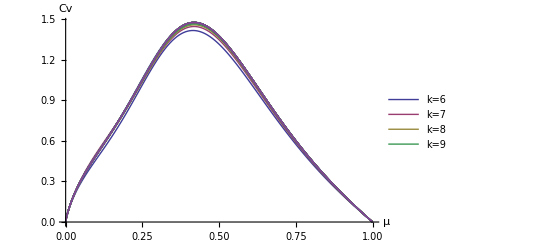

```mathematica
Clear[η,μ,Cvμc, kVectorc]
precN=500;
InitRGΩ;
dμdβ=-4 μ;
d2μdβ2=16 μ;
dA0dμ=Table[D[A[i]/.SAT,μ],{i,0,dim-1}];
d2A0dμ2=D[dA0dμ,μ];
η=N[1.0, precN];
(**Temperature for Cv, X**)
Tmin=0.01;
Tmax=10.01;
Tinc=0.04;
TVector=N[Range[Tmin,Tmax,Tinc],precN];
μVector=N[Exp[2/TVector],precN];
μinvVector=1.0/μVector;
μiv=Range[Ceiling[Exp[-Max[2.0/Max[TVector]]]*1000]/1000.0,0.999999,0.005];
μiv=N[Join[μiv,{0.999999998}],precN];
μinvVector=N[Join[μinvVector,μiv],precN];
μVector=N[Join[μVector,1.0/μiv],precN];
μVector[[Dimensions[μVector][[1]]]]=1;
TVector=N[Join[TVector,2.0/Log[1/μiv]],precN];
Clear[μiv]
kVector=Range[6,32,1];
Cvμ=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];(*Magnetization at different H at μ=0.01*);
μind=0;
Do[
kind=1;
μind++;
(*Save results in the middle*)
If[Mod[μind,100]==0,Print[N[μind/Dimensions[μVector][[1]],4]," Completed."];
Clear[Cvμc,kVectorc];
kVectorc=kVector;
Cvμc=Cvμ;
PrependTo[Cvμc,TVector];
PrependTo[Cvμc,μinvVector];
PrependTo[kVectorc,0];
PrependTo[kVectorc,0];
Cvμc=Transpose[Cvμc];
Cvμc=PrependTo[Cvμc,kVectorc];
Export["/home/xcheng0907/GoogleDrive/Research/AntiHN/Maca/data/HNNP_AFM_Cv_pre_k6_32_the.csv",Cvμc];
];
(*Save results in the middle*)
Clear[μ];
InitRGΩ;
μ=N[μVector[[μind]],precN];
For[i=3,i≤Max[kVector],++i,
RGΩ;
If[i==kVector[[kind]],
DlnZ=N[DLnZ1/.SAT,precN];
DDlnZ=N[D2LnZ1/.SAT,precN];
term0=N[(dμdβ)^2*(d2A0dμ2.Υ).DlnZ,precN];
term1=N[d2μdβ2*(dA0dμ.Υ).DlnZ,precN];
term2=N[dμdβ^2*(dA0dμ.(Λ.DlnZ).dA0dμ),precN];
term3=N[dμdβ^2*(dA0dμ.Υ).((dA0dμ.Υ).DDlnZ),precN];
Part[Part[Cvμ,kind],μind]=N[(term0+term1+term2+term3)/(2^i+1)/TVector[[μind]],precN];
kind++,
];
],
{μi,1,Dimensions[μVector][[1]],1}
];
ListLinePlot[Table[Table[{μinvVector[[i]],Cvμ[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,Dimensions[Cvμ][[1]]}],PlotLegends->{"k=6","k=7","k=8","k=9"},PlotStyle->Thick,AxesLabel->{"μ","Cv"}]
Clear[Cvμc,kVectorc];
Cvμc=Cvμ;
kVectorc=kVector;
PrependTo[Cvμc,TVector];
PrependTo[Cvμc,μinvVector];
PrependTo[kVectorc,0];
PrependTo[kVectorc,0];
Cvμc=Transpose[Cvμc];
Cvμc=PrependTo[Cvμc,kVectorc];
Export["/home/xcheng0907/GoogleDrive/Research/AntiHN/Maca/data/HNNP_AFM_Cv_pre_k6_32_the.csv",Cvμc];(*For Linux*)
(*Export["C:/Users/sxcheng/Google Drive/Research/AntiHN/Maca/data/HNNP_AFM_Cv_k6_32.csv,Cvμc](*For Windows*)*)
```

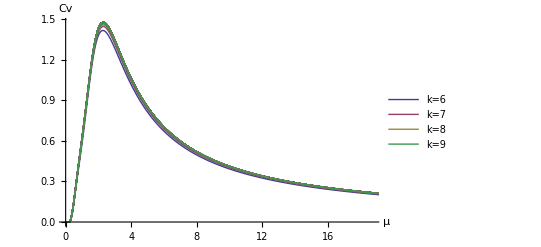

```mathematica
Tmin=0.01;
Tmax=10.01;
Tinc=0.01;
TVector=N[Range[Tmin,Tmax,Tinc],precN];
μVector=N[Exp[2/TVector],precN];
μinvVector=1.0/μVector;
μiv=Range[Ceiling[Exp[-Max[2.0/Max[TVector]]]*1000]/1000.0,0.999999,0.005];
μiv=N[Join[μiv,{0.999999998}],precN];
μinvVector=N[Join[μinvVector,μiv],precN];
μVector=N[Join[μVector,1.0/μiv],precN];
μVector[[Dimensions[μVector][[1]]]]=1;
TVector=N[Join[TVector,2.0/Log[1/μiv]],precN];
Clear[μiv]
ListLinePlot[Table[Table[{TVector[[i]],Cvμ[[j]][[i]]},{i,1,Dimensions[μVector][[1]]}],{j,1,Dimensions[Cvμ][[1]]}],PlotLegends->{"k=6","k=7","k=8","k=9"},PlotStyle->Thick,AxesLabel->{"μ","Cv"}]
```

4.2 Binder Cumulant U4

```mathematica
Clear[η,μ,T]
InitRGΩ
dηdH=-2 η;
d2ηdH2=4 η;
dA0dη=Table[D[A[i]/.SAT,η],{i,0,dim-1}];
d2A0dη2=D[dA0dη,η];
DlnZ=Simplify[(DLnZ1/.SAT),μ>0&&η>0];
DDlnZ=Simplify[(D2LnZ1/.SAT),μ>0&&η>0];
term0=Factor[(dηdH)^2*(d2A0dη2.Υ).DlnZ];
term1=Factor[d2ηdH2*(dA0dη.Υ).DlnZ];
term2=Factor[dηdH^2*(dA0dη.(Λ.DlnZ).dA0dη)];
term3=Factor[dηdH^2*(dA0dη.Υ).((dA0dη.Υ).DDlnZ)];
Simplify[Factor[dηdH^2*D[Log[Z[1]],{η,2}]+d2ηdH2*D[Log[Z[1]],{η,1}]]/.{η->1}]
Simplify[Factor[(term0+term1+term2+term3)]/.{η->1},Assumptions->{μ>0}]
Simplify[Factor[D[Factor[dηdH*D[Log[Z[1]],η]],η]*dηdH]/.{η->1}]
```

(9+2 μ+μ^2)/(1+μ)^2

(9+2 μ+μ^2)/(1+μ)^2

(9+2 μ+μ^2)/(1+μ)^2

```mathematica
Clear[η,μ,T]
InitRGΩ;
μ=0.1
RGΩ;y
dηdH=-2 η;
d2ηdH2=4 η
dA0dη=Table[D[A[i]/.SAT,η],{i,0,dim-1}];
d2A0dη2=D[dA0dη,η];
DlnZ=Simplify[(DLnZ1/.SAT),μ>0&&η>0];
DDlnZ=Simplify[(D2LnZ1/.SAT),μ>0&&η>0];
dηdH^2*D[Log[Z[2]],{η,2}]+d2ηdH2*D[Log[Z[2]],{η,1}]/.{η->1}
D[dηdH*D[Log[Z[2]],η],η]*dηdH/.{η->1}
η=1
term0=(dηdH)^2*(d2A0dη2.Υ).DlnZ
term1=d2ηdH2*(dA0dη.Υ).DlnZ;
term2=dηdH^2*(dA0dη.(Λ.DlnZ).dA0dη);
term3=dηdH^2*(dA0dη.Υ).((dA0dη.Υ).DDlnZ);
(term0+term1+term2+term3)
Clear[μ,η];
```

0.1

4 η

$Aborted

24.3612

24.3612

1

0.263373

73.2077

<m^2> test:

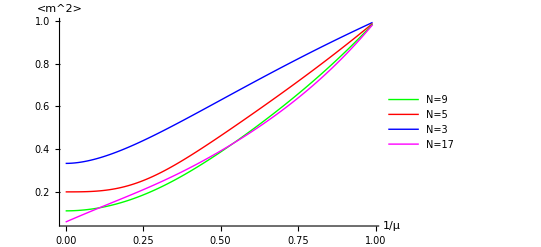

```mathematica
Clear[μ,η]
μinvV=Range[0.0001, 1,0.01];
m2Z=Z[1];
m21=1/m2Z*D[m2Z,{η,2}]*(dηdH)^2/.{η->1};
pm21=ListLinePlot[Table[{μinvV[[i]],N[m21/3.0/.{μ->(1.0/μinvV[[i]])}]},{i,1,Dimensions[μinvV][[1]]}], AxesLabel->{"1/μ","<m^2>"},PlotStyle->{Blue},PlotLegends->{"N=3"}];

m2Z=Z[2];
m21=1/m2Z*D[m2Z,{η,2}]*(dηdH)^2/.{η->1};
pm22=ListLinePlot[Table[{μinvV[[i]],N[m21/5.0/.{μ->(1.0/μinvV[[i]])}]},{i,1,Dimensions[μinvV][[1]]}], AxesLabel->{"1/μ","<m^2>"},PlotStyle->{Red},PlotLegends->{"N=5"}];

m2Z=Z[3];
m21=1/m2Z*D[m2Z,{η,2}]*(dηdH)^2/.{η->1};
pm23=ListLinePlot[Table[{μinvV[[i]],N[m21/9.0/.{μ->(1.0/μinvV[[i]])}]},{i,1,Dimensions[μinvV][[1]]}], AxesLabel->{"1/μ","<m^2>"},PlotStyle->{Green},PlotLegends->{"N=9"},AxesOrigin->{0,0}];


m2Z=Z[4];
m21=1/m2Z*D[m2Z,{η,2}]*(dηdH)^2/.{η->1};
pm24=ListLinePlot[Table[{μinvV[[i]],N[m21/17.0/.{μ->(1.0/μinvV[[i]])}]},{i,1,Dimensions[μinvV][[1]]}], AxesLabel->{"1/μ","<m^2>"},PlotStyle->{Magenta},PlotLegends->{"N=17"}];
Show[pm21, pm22, pm23, pm24,PlotRange->All,AxesOrigin->{0,0}]
```

<m^2> test 2:

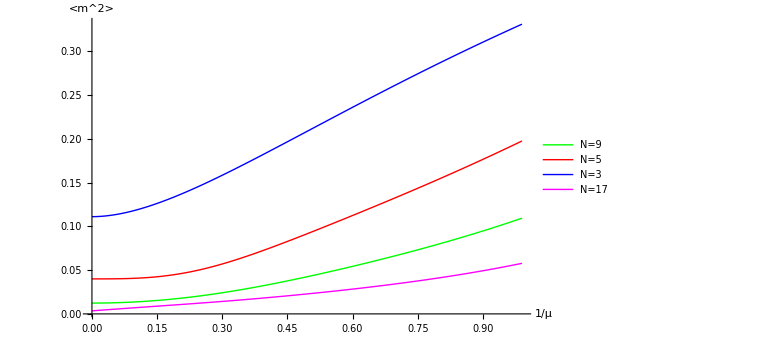

```mathematica
Clear[μ,η]
μinvV=Range[0.0001, 1,0.01];
m2Z=Z[1];
m21=1/m2Z*(dηdH)*(D[m2Z,{η,2}]*dηdH+D[m2Z,{η,1}]*D[dηdH,{η,1}])/.{η->1};
pm21=ListLinePlot[Table[{μinvV[[i]],N[m21/3.0^2/.{μ->(1.0/μinvV[[i]])}]},{i,1,Dimensions[μinvV][[1]]}], AxesLabel->{"1/μ","<m^2>"},PlotStyle->{Blue},PlotLegends->{"N=3"}];

m2Z=Z[2];
m21=1/m2Z*D[D[m2Z,{η,1}]*(dηdH),η]*(dηdH)/.{η->1};
pm22=ListLinePlot[Table[{μinvV[[i]],N[m21/5.0^2/.{μ->(1.0/μinvV[[i]])}]},{i,1,Dimensions[μinvV][[1]]}], AxesLabel->{"1/μ","<m^2>"},PlotStyle->{Red},PlotLegends->{"N=5"}];

m2Z=Z[3];
m21=1/m2Z*D[D[m2Z,{η,1}]*(dηdH),η]*(dηdH)/.{η->1};
pm23=ListLinePlot[Table[{μinvV[[i]],N[m21/9.0^2/.{μ->(1.0/μinvV[[i]])}]},{i,1,Dimensions[μinvV][[1]]}], AxesLabel->{"1/μ","<m^2>"},PlotStyle->{Green},PlotLegends->{"N=9"},AxesOrigin->{0,0}];


m2Z=Z[4];
m21=1/m2Z*D[D[m2Z,{η,1}]*(dηdH),η]*(dηdH)/.{η->1};
pm24=ListLinePlot[Table[{μinvV[[i]],N[m21/17.0^2/.{μ->(1.0/μinvV[[i]])}]},{i,1,Dimensions[μinvV][[1]]}], AxesLabel->{"1/μ","<m^2>"},PlotStyle->{Magenta},PlotLegends->{"N=17"}];
Show[pm21, pm22, pm23, pm24,PlotRange->All,AxesOrigin->{0,0}]
```

<m^2> test 3:

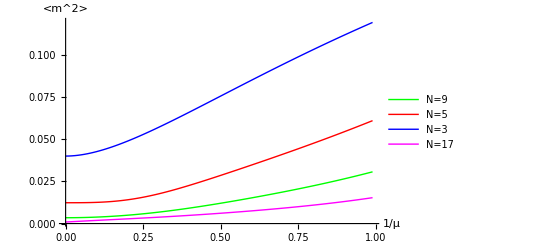

```mathematica
Clear[μ,η]
μinvV=Range[0.0001, 1,0.01];
m2Z=Z[1];
m21=1/m2Z*(dηdH)*(D[m2Z,{η,2}]*dηdH+D[m2Z,{η,1}]*D[dηdH,{η,1}])/.{η->1};
m2[1]=Table[N[m21/5.0^2/.{μ->(1.0/μinvV[[i]])}],{i,1,Dimensions[μinvV][[1]]}];
pm21=ListLinePlot[Table[{μinvV[[i]],N[m21/5.0^2/.{μ->(1.0/μinvV[[i]])}]},{i,1,Dimensions[μinvV][[1]]}], AxesLabel->{"1/μ","<m^2>"},PlotStyle->{Blue},PlotLegends->{"N=3"}];

m2Z=Z[2];
m21=1/m2Z*D[D[m2Z,{η,1}]*(dηdH),η]*(dηdH)/.{η->1};
m2[2]=Table[N[m21/9.0^2/.{μ->(1.0/μinvV[[i]])}],{i,1,Dimensions[μinvV][[1]]}];
pm22=ListLinePlot[Table[{μinvV[[i]],N[m21/9.0^2/.{μ->(1.0/μinvV[[i]])}]},{i,1,Dimensions[μinvV][[1]]}], AxesLabel->{"1/μ","<m^2>"},PlotStyle->{Red},PlotLegends->{"N=5"}];

m2Z=Z[3];
m21=1/m2Z*D[D[m2Z,{η,1}]*(dηdH),η]*(dηdH)/.{η->1};
m2[3]=Table[N[m21/17.0^2/.{μ->(1.0/μinvV[[i]])}],{i,1,Dimensions[μinvV][[1]]}];
pm23=ListLinePlot[Table[{μinvV[[i]],N[m21/17.0^2/.{μ->(1.0/μinvV[[i]])}]},{i,1,Dimensions[μinvV][[1]]}], AxesLabel->{"1/μ","<m^2>"},PlotStyle->{Green},PlotLegends->{"N=9"},AxesOrigin->{0,0}];


m2Z=Z[4];
m21=1/m2Z*D[D[m2Z,{η,1}]*(dηdH),η]*(dηdH)/.{η->1};
m2[4]=Table[N[m21/33.0^2/.{μ->(1.0/μinvV[[i]])}],{i,1,Dimensions[μinvV][[1]]}];
pm24=ListLinePlot[Table[{μinvV[[i]],N[m21/33.0^2/.{μ->(1.0/μinvV[[i]])}]},{i,1,Dimensions[μinvV][[1]]}], AxesLabel->{"1/μ","<m^2>"},PlotStyle->{Magenta},PlotLegends->{"N=17"}];
Show[pm21, pm22, pm23, pm24,PlotRange->All,AxesOrigin->{0,0}]
```

<m^4> test 1:

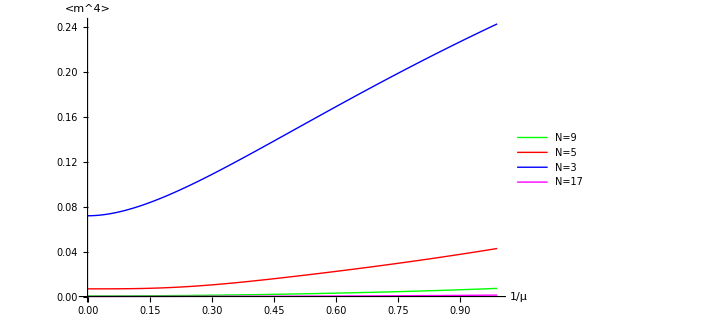

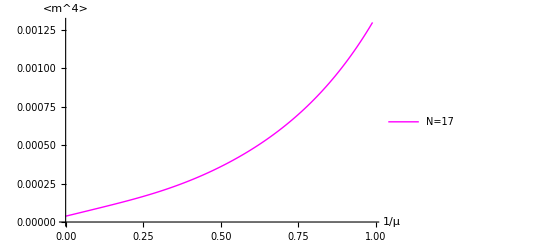

```mathematica
Clear[μ,η]
μinvV=Range[0.0001, 1,0.01];
m2Z=Z[1];
m21=1/m2Z*D[m2Z,{η,4}]*(dηdH)^4/.{η->1};
m4[1]=Table[N[m21/5.0^4/.{μ->(1.0/μinvV[[i]])}],{i,1,Dimensions[μinvV][[1]]}];
pm21=ListLinePlot[Table[{μinvV[[i]],N[m21/5.0^4/.{μ->(1.0/μinvV[[i]])}]},{i,1,Dimensions[μinvV][[1]]}], AxesLabel->{"1/μ","<m^4>"},PlotStyle->{Blue},PlotLegends->{"N=3"}];

m2Z=Z[2];
m21=1/m2Z*D[m2Z,{η,4}]*(dηdH)^4/.{η->1};
m4[2]=Table[N[m21/9.0^4/.{μ->(1.0/μinvV[[i]])}],{i,1,Dimensions[μinvV][[1]]}];
pm22=ListLinePlot[Table[{μinvV[[i]],N[m21/9.0^4/.{μ->(1.0/μinvV[[i]])}]},{i,1,Dimensions[μinvV][[1]]}], AxesLabel->{"1/μ","<m^2>"},PlotStyle->{Red},PlotLegends->{"N=5"}];

m2Z=Z[3];
m21=1/m2Z*D[m2Z,{η,4}]*(dηdH)^4/.{η->1};
m4[3]=Table[N[m21/17.0^4/.{μ->(1.0/μinvV[[i]])}],{i,1,Dimensions[μinvV][[1]]}];
pm23=ListLinePlot[Table[{μinvV[[i]],N[m21/17.0^4/.{μ->(1.0/μinvV[[i]])}]},{i,1,Dimensions[μinvV][[1]]}], AxesLabel->{"1/μ","<m^4>"},PlotStyle->{Green},PlotLegends->{"N=9"},AxesOrigin->{0,0}];


m2Z=Z[4];
m21=1/m2Z*D[m2Z,{η,4}]*(dηdH)^4/.{η->1};
m4[4]=Table[N[m21/33.0^4/.{μ->(1.0/μinvV[[i]])}],{i,1,Dimensions[μinvV][[1]]}];
pm24=ListLinePlot[Table[{μinvV[[i]],N[m21/33.0^4/.{μ->(1.0/μinvV[[i]])}]},{i,1,Dimensions[μinvV][[1]]}], AxesLabel->{"1/μ","<m^4>"},PlotStyle->{Magenta},PlotLegends->{"N=17"}];
Show[pm21, pm22, pm23, pm24,PlotRange->All,AxesOrigin->{0,0}]
Show[pm24]
```

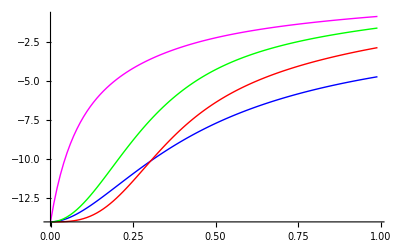

```mathematica
pb1=ListLinePlot[Table[{μinvV[[i]],(1-m4[1]/m2[1]^2/3.0)[[i]]},{i,1,Dimensions[μinvV][[1]]}],PlotStyle->{Blue}];
pb2=ListLinePlot[Table[{μinvV[[i]],(1-m4[2]/m2[2]^2/3.0)[[i]]},{i,1,Dimensions[μinvV][[1]]}],PlotStyle->{Red}];
pb3=ListLinePlot[Table[{μinvV[[i]],(1-m4[3]/m2[3]^2/3.0)[[i]]},{i,1,Dimensions[μinvV][[1]]}],PlotStyle->{Green}];
pb4=ListLinePlot[Table[{μinvV[[i]],(1-m4[4]/m2[4]^2/3.0)[[i]]},{i,1,Dimensions[μinvV][[1]]}],PlotStyle->{Magenta}];
Show[pb1,pb2,pb3,pb4,PlotRange->All]
```

4.2 Susceptibility χ

Test susceptibility

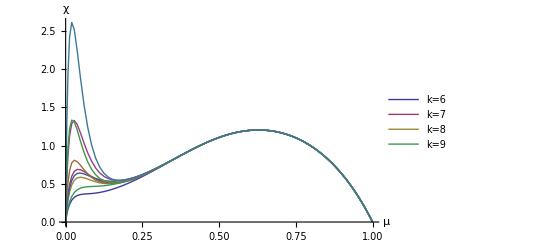

```mathematica
(************************* χ at H=0 ****************************)
Clear[η,μ,χμ,χμc]
H=0;
kVector=Range[8,16,1];
precN=1000;
Tmin=0.01;
Tmax=10.01;
Tinc=0.05;
TVector=N[Range[Tmin,Tmax,Tinc],precN];
μVector=N[Exp[2/TVector],precN];
μinvVector=1.0/μVector;
μiv=Range[Ceiling[Exp[-Max[2.0/Max[TVector]]]*1000]/1000.0,0.999999,0.005];
μiv=N[Join[μiv,{0.999999998}],precN];
μinvVector=N[Join[μinvVector,μiv],precN];
μVector=N[Join[μVector,1.0/μiv],precN];
μVector[[Dimensions[μVector][[1]]]]=1;
TVector=N[Join[TVector,2.0/Log[1/μiv]],precN];
Clear[μiv]
InitRGΩ;
dμdβ=-2 μ;
d2μdβ2=4 μ;
dηdH=-2 η;
d2ηdH2=4 η;
dA0dμ=dμdβ*Table[D[A[i]/.SAT,μ],{i,0,dim-1}];
dηdH=-2η;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
d2A0dμ2=D[dA0dμ,μ];
d2A0dη2=D[dA0dη,η];
χμ=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];
η=N[1,precN];
μind=0;
kind=1;
Do[kind=1;
++μind;
Clear[μ];
InitRGΩ;
μ=μVector[[μind]];
For[i=2,i≤Max[kVector],++i,RGΩ;
If[i==kVector[[kind]],
DlnZ=DLnZ1/.SAT;
DDlnZ=D2LnZ1/.SAT;
term0=N[(dηdH)^2*(d2A0dη2.Υ).DlnZ,precN];
term1=N[d2ηdH2*(dA0dη.Υ).DlnZ,precN];
term2=N[dηdH^2*(dA0dη.(Λ.DlnZ).dA0dη),precN];
term3=N[dηdH^2*(dA0dη.Υ).((dA0dη.Υ).DDlnZ),precN];
Part[Part[χμ,kind],μind]=N[(term0+term1+term2+term3)/(2^i+1)/μVector[[μind]]*4.0/TVector[[μind]],20];++kind,];],{μi,1,Dimensions[μVector][[1]],1}];
ListLinePlot[Table[Table[{μinvVector[[i]],χμ[[j]][[i]]},{i,1,Dimensions[μinvVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=6","k=7","k=8","k=9"},PlotStyle->Thick,AxesLabel->{"μ","χ"}]
χμc=χμ;
kVectorc=kVector;
PrependTo[χμc,TVector];
PrependTo[χμc,μinvVector];
PrependTo[kVectorc,0];
PrependTo[kVectorc,0];
χμc=Transpose[χμc];
χμc=PrependTo[χμc,kVectorc];
Export["/home/xcheng0907/GoogleDrive/Research/AntiHN/Maca/data/HNNP_AFM_X_pre.csv",χμc];(*For Linux*)
(*Export["C:/Users/sxcheng/Google Drive/Research/AntiHN/Maca/data/HNNP_AFM_X_test.csv,χμc](*For Windows*)*)
```

```mathematica
ListLinePlot[Table[Table[{μinvVector[[i]],χμ[[j]][[i]]/TVector[[i]]^2},{i,1,Dimensions[μinvVector][[1]]}],{j,1,9}],PlotLegends->{"k=6","k=7","k=8","k=9"},PlotStyle->Thick,AxesLabel->{"μ","χ"}]
```

-Graphics-

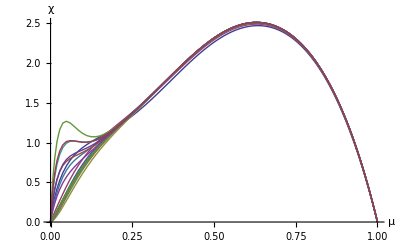

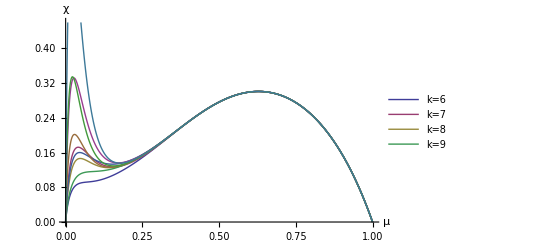

```mathematica
Clear[η,μ,χμ,χμc]
H=0;
kVector=Range[8,16,1];
precN=1000;
Tmin=0.01;
Tmax=10.01;
Tinc=0.01;
TVector=N[Range[Tmin,Tmax,Tinc],precN];
μVector=N[Exp[2/TVector],precN];
μinvVector=1.0/μVector;
μiv=Range[Ceiling[Exp[-Max[2.0/Max[TVector]]]*1000]/1000.0,0.999999,0.005];
μiv=N[Join[μiv,{0.999999998}],precN];
μinvVector=N[Join[μinvVector,μiv],precN];
μVector=N[Join[μVector,1.0/μiv],precN];
μVector[[Dimensions[μVector][[1]]]]=1;
TVector=N[Join[TVector,2.0/Log[1/μiv]],precN];
Clear[μiv]
InitRGΩ;
dμdβ=-2 μ;
d2μdβ2=4 μ;
dηdH=-2 η;
d2ηdH2=4 η;
dA0dμ=dμdβ*Table[D[A[i]/.SAT,μ],{i,0,dim-1}];
dηdH=-2η;
dA0dη=dηdH*Table[D[A[i]/.SAT,η],{i,0,dim-1}];
d2A0dμ2=D[dA0dμ,μ];
d2A0dη2=D[dA0dη,η];
χμ=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];
η=N[1,precN];
μind=0;
kind=1;
Do[kind=1;
++μind;
Clear[μ];
InitRGΩ;
μ=μVector[[μind]];
For[i=2,i≤Max[kVector],++i,RGΩ;
If[i==kVector[[kind]],
DlnZ=DLnZ1/.SAT;
DDlnZ=D2LnZ1/.SAT;
term0=N[(dηdH)^2*(d2A0dη2.Υ).DlnZ,precN];
term1=N[d2ηdH2*(dA0dη.Υ).DlnZ,precN];
term2=N[dηdH^2*(dA0dη.(Λ.DlnZ).dA0dη),precN];
term3=N[dηdH^2*(dA0dη.Υ).((dA0dη.Υ).DDlnZ),precN];
Part[Part[χμ,kind],μind]=N[(term0+term1+term2+term3)/(2^i+1)/μVector[[μind]]/TVector[[μind]],20];++kind,];],{μi,1,Dimensions[μVector][[1]],1}];
ListLinePlot[Table[Table[{μinvVector[[i]],χμ[[j]][[i]]},{i,1,Dimensions[μinvVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=6","k=7","k=8","k=9"},PlotStyle->Thick,AxesLabel->{"μ","χ"}]
χμc=χμ;
kVectorc=kVector;
PrependTo[χμc,TVector];
PrependTo[χμc,μinvVector];
PrependTo[kVectorc,0];
PrependTo[kVectorc,0];
χμc=Transpose[χμc];
χμc=PrependTo[χμc,kVectorc];
Export["/home/xcheng0907/GoogleDrive/Research/AntiHN/Maca/data/HNNP_AFM_X_pre.csv",χμc];(*For Linux*)
(*Export["C:/Users/sxcheng/Google Drive/Research/AntiHN/Maca/data/HNNP_AFM_X_test.csv,χμc](*For Windows*)*)
```

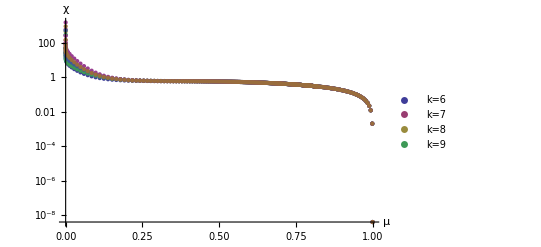

```mathematica
ListLogPlot[Table[Table[{μinvVector[[i]],χμ[[j]][[i]]},{i,1,Dimensions[μinvVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=6","k=7","k=8","k=9"},PlotStyle->Thick,AxesLabel->{"μ","χ"},PlotRange->All]
```

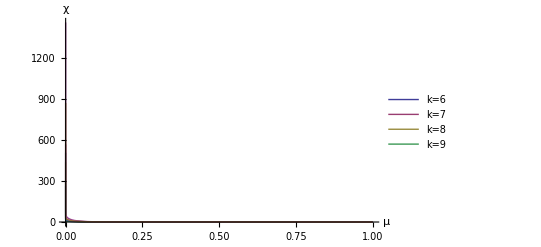

```mathematica
ListLinePlot[Table[Table[{μinvVector[[i]],χμ[[j]][[i]]},{i,1,Dimensions[μinvVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=6","k=7","k=8","k=9"},PlotStyle->Thick,AxesLabel->{"μ","χ"},PlotRange->]
```

```mathematica
ListLogPlot[Table[Table[{μinvVector[[i]],χμ[[j]][[i]]},{i,1,Dimensions[μinvVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=6","k=7","k=8","k=9"},PlotStyle->Thick,AxesLabel->{"μ","χ"}]
ListLogPlot[Table[Table[{TVector[[i]],χμ[[j]][[i]]},{i,1,Dimensions[μinvVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=6","k=7","k=8","k=9"},PlotStyle->Thick,AxesLabel->{"T","χ"}]
```

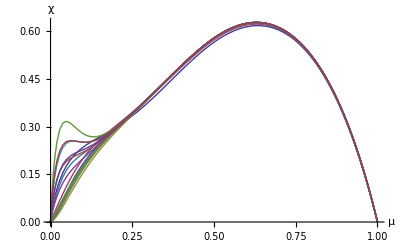

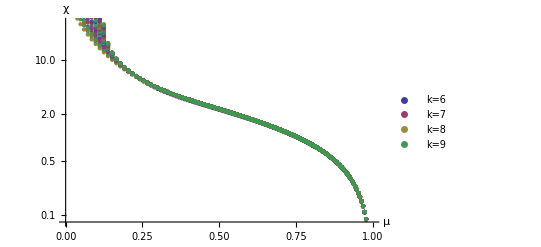

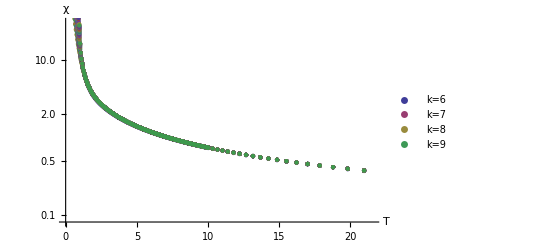

```mathematica
(************************* χ at H=10^(-4) ****************************)
(**Temperature for Cv,X**)
Clear[η,μ,χμ,χμc]
H=10^(-4);
precN=1000;
Tmin=0.01;
Tmax=10.01;
Tinc=0.01;
TVector=N[Range[Tmin,Tmax,Tinc],precN];
μVector=Exp[2/TVector];
μinvVector=1.0/μVector;
μiv=Range[Ceiling[Exp[-Max[2.0/Max[TVector]]]*1000]/1000.0,0.999999,0.005];
μinvVector=N[Join[μinvVector,μiv],precN];
μVector=N[Join[μVector,1.0/μiv],precN];
μiv[[Dimensions[μiv][[1]]]]=N[0.99999998,10];
TVector=N[Join[TVector,2.0/Log[1/μiv]],precN];
kVector=Range[6,128,1];
Clear[μiv]
InitRGΩ;
dμdβ=-4 μ;
d2μdβ2=16 μ;
dA0dμ=Table[D[A[i]/.SAT,μ],{i,0,dim-1}];
d2A0dμ2=D[dA0dμ,μ];
dηdH=-2 η;
d2ηdH2=4 η;
dA0dη=Table[D[A[i]/.SAT,η],{i,0,dim-1}];
d2A0dη2=D[dA0dη,η];
χμ=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];
η=N[Exp[-H],precN];
μind=0;
kind=1;
Do[kind=1;
++μind;
Clear[μ];
InitRGΩ;
μ=μVector[[μind]];
For[i=3,i≤Max[kVector],++i,RGΩ;
If[i==kVector[[kind]],DlnZ=DLnZ1/.SAT;
DDlnZ=D2LnZ1/.SAT;
term0=Factor[(dηdH)^2*(d2A0dη2.Υ).DlnZ];
term1=Factor[d2ηdH2*(dA0dη.Υ).DlnZ];
term2=Factor[dηdH^2*(dA0dη.(Λ.DlnZ).dA0dη)];
term3=Factor[dηdH^2*(dA0dη.Υ).((dA0dη.Υ).DDlnZ)];
Part[Part[χμ,kind],μind]=N[(term0+term1+term2+term3)/(2^i+1),20];++kind,];],{μi,1,Dimensions[μVector][[1]],1}];
Rasterize[ListLinePlot[Table[Table[{μinvVector[[i]],χμ[[j]][[i]]},{i,1,Dimensions[μinvVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=8","k=12","k=16","k=32"},PlotStyle->Thick,AxesLabel->{"μ","χ"}]]
χμc=χμ;
PrependTo[χμc,TVector];
PrependTo[χμc,μinvVector];
PrependTo[kVector,0];
PrependTo[kVector,0];
χμc=Transpose[χμc];
χμc=PrependTo[χμc,kVector];
Export["/home/xcheng0907/GoogleDrive/Research/AntiHN/Maca/data/HNNP_AFM_X_H1e-4.csv",χμc];
```

-Graphics-

```mathematica
(************************* χ at H=10^(-8) ****************************)
(**Temperature for Cv,X**)
Clear[η,μ,χμ,χμc]
H=10^(-8);
precN=1000;
Tmin=0.01;
Tmax=10.01;
Tinc=0.01;
TVector=N[Range[Tmin,Tmax,Tinc],precN];
μVector=Exp[2/TVector];
μinvVector=1.0/μVector;
μiv=Range[Ceiling[Exp[-Max[2.0/Max[TVector]]]*1000]/1000.0,0.999999,0.005];
μinvVector=N[Join[μinvVector,μiv],precN];
μVector=N[Join[μVector,1.0/μiv],precN];
μiv[[Dimensions[μiv][[1]]]]=N[0.99999998,10];
TVector=N[Join[TVector,2.0/Log[1/μiv]],precN];
kVector=Range[6,128,1];
Clear[μiv]
InitRGΩ;
dμdβ=-4 μ;
d2μdβ2=16 μ;
dA0dμ=Table[D[A[i]/.SAT,μ],{i,0,dim-1}];
d2A0dμ2=D[dA0dμ,μ];
dηdH=-2 η;
d2ηdH2=4 η;
dA0dη=Table[D[A[i]/.SAT,η],{i,0,dim-1}];
d2A0dη2=D[dA0dη,η];
χμ=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];
η=N[Exp[-H],precN];
μind=0;
kind=1;
Do[kind=1;
++μind;
Clear[μ];
InitRGΩ;
μ=μVector[[μind]];
For[i=3,i≤Max[kVector],++i,RGΩ;
If[i==kVector[[kind]],DlnZ=DLnZ1/.SAT;
DDlnZ=D2LnZ1/.SAT;
term0=Factor[(dηdH)^2*(d2A0dη2.Υ).DlnZ];
term1=Factor[d2ηdH2*(dA0dη.Υ).DlnZ];
term2=Factor[dηdH^2*(dA0dη.(Λ.DlnZ).dA0dη)];
term3=Factor[dηdH^2*(dA0dη.Υ).((dA0dη.Υ).DDlnZ)];
Part[Part[χμ,kind],μind]=N[(term0+term1+term2+term3)/(2^i+1),20];++kind,];],{μi,1,Dimensions[μVector][[1]],1}];
Rasterize[ListLinePlot[Table[Table[{μinvVector[[i]],χμ[[j]][[i]]},{i,1,Dimensions[μinvVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=8","k=12","k=16","k=32"},PlotStyle->Thick,AxesLabel->{"μ","χ"}]]
χμc=χμ;
PrependTo[χμc,TVector];
PrependTo[χμc,μinvVector];
PrependTo[kVector,0];
PrependTo[kVector,0];
χμc=Transpose[χμc];
χμc=PrependTo[χμc,kVector];
Export["/home/xcheng0907/GoogleDrive/Research/AntiHN/Maca/data/HNNP_AFM_X_H1e-8.csv",χμc];
```

-Graphics-

```mathematica
(************************* χ at H=10^(-16) ****************************)
(**Temperature for Cv,X**)
Clear[η,μ,χμ,χμc]
H=10^(-16);
precN=1000;
Tmin=0.01;
Tmax=10.01;
Tinc=0.01;
TVector=N[Range[Tmin,Tmax,Tinc],precN];
μVector=Exp[2/TVector];
μinvVector=1.0/μVector;
μiv=Range[Ceiling[Exp[-Max[2.0/Max[TVector]]]*1000]/1000.0,0.999999,0.005];
μinvVector=N[Join[μinvVector,μiv],precN];
μVector=N[Join[μVector,1.0/μiv],precN];
μiv[[Dimensions[μiv][[1]]]]=N[0.99999998,10];
TVector=N[Join[TVector,2.0/Log[1/μiv]],precN];
kVector=Range[6,128,1];
Clear[μiv]
InitRGΩ;
dμdβ=-4 μ;
d2μdβ2=16 μ;
dA0dμ=Table[D[A[i]/.SAT,μ],{i,0,dim-1}];
d2A0dμ2=D[dA0dμ,μ];
dηdH=-2 η;
d2ηdH2=4 η;
dA0dη=Table[D[A[i]/.SAT,η],{i,0,dim-1}];
d2A0dη2=D[dA0dη,η];
χμ=ConstantArray[0,{Dimensions[kVector][[1]],Dimensions[μVector][[1]]}];
η=N[Exp[-H],precN];
μind=0;
kind=1;
Do[kind=1;
++μind;
Clear[μ];
InitRGΩ;
μ=μVector[[μind]];
For[i=3,i≤Max[kVector],++i,RGΩ;
If[i==kVector[[kind]],DlnZ=DLnZ1/.SAT;
DDlnZ=D2LnZ1/.SAT;
term0=Factor[(dηdH)^2*(d2A0dη2.Υ).DlnZ];
term1=Factor[d2ηdH2*(dA0dη.Υ).DlnZ];
term2=Factor[dηdH^2*(dA0dη.(Λ.DlnZ).dA0dη)];
term3=Factor[dηdH^2*(dA0dη.Υ).((dA0dη.Υ).DDlnZ)];
Part[Part[χμ,kind],μind]=N[(term0+term1+term2+term3)/(2^i+1),20];++kind,];],{μi,1,Dimensions[μVector][[1]],1}];
Rasterize[ListLinePlot[Table[Table[{μinvVector[[i]],χμ[[j]][[i]]},{i,1,Dimensions[μinvVector][[1]]}],{j,1,Dimensions[kVector][[1]]}],PlotLegends->{"k=8","k=12","k=16","k=32"},PlotStyle->Thick,AxesLabel->{"μ","χ"}]]
χμc=χμ;
PrependTo[χμc,TVector];
PrependTo[χμc,μinvVector];
PrependTo[kVector,0];
PrependTo[kVector,0];
χμc=Transpose[χμc];
χμc=PrependTo[χμc,kVector];
Export["/home/xcheng0907/GoogleDrive/Research/AntiHN/Maca/data/HNNP_AFM_X_H1e-16.csv",χμc];
```

-Graphics-